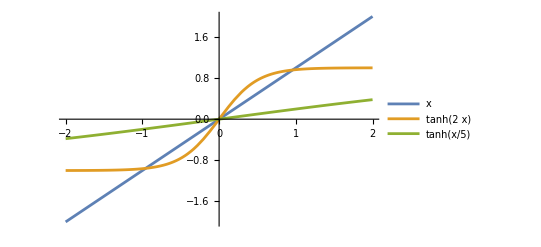

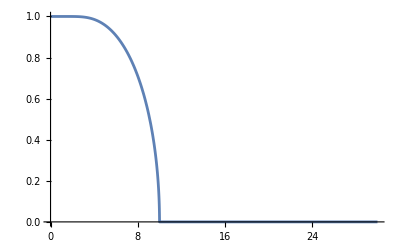

```mathematica
Plot[{x,Tanh[2x],Tanh[x/5]},{x,-2,2},PlotLegends->"Expressions"]


f[b_]:=FindRoot[m-Tanh[10m/b],{m,1}][[1,2]]

Plot[f[b],{b,0,30}]
```